## EdgeLengths-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 09:07:51
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

Generate a random template constrained to  circle of radius 100 with at least 50 cells.  The actual number of cells will be the smallest integer square larger than 50.

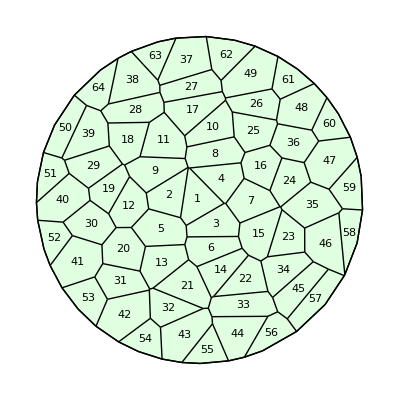

```mathematica
w=TemplateRandomCircularGrid[50,100];
ShowTissue[w, "CellNumbers"-> True]
```

```mathematica
EdgeLengths[w]
```

{2.1506,35.5381,11.7634,10.0311,21.2154,15.6003,8.52036,28.8041,14.9253,26.8688,18.9381,22.8202,9.26431,9.77663,7.46903,25.5566,13.9689,9.50729,15.7467,21.131,8.66728,6.29126,11.4928,13.667,23.2442,26.2551,17.9406,14.0698,25.41,32.3704,28.55,9.66656,26.1394,13.6895,9.33431,1.4669,7.67924,10.6346,14.3094,14.457,15.5675,15.4776,12.5545,21.8126,27.7009,24.1448,9.82142,30.0601,20.2459,0.643759,17.2664,10.9735,2.04806,8.30293,24.2237,27.9298,33.172,3.34803,28.042,23.9584,4.32174,33.3042,6.57063,28.5797,19.4614,6.09543,36.4091,19.0738,5.87847,31.0578,6.92808,33.1347,4.86342,9.5615,7.17641,5.70906,6.99917,26.944,29.6188,31.5154,0.136267,0.815021,6.59486,30.293,31.6721,20.947,29.9092,3.13123,6.69453,5.66281,1.45835,8.78815,20.4416,4.34337,34.28,30.2326,24.7359,33.1606,33.5041,6.85438,29.5959,4.32597,0.98308,1.41265,29.0175,8.23655,14.7256,19.0643,15.2853,27.5452,11.6248,8.26902,7.57653,26.4942,9.70862,6.77588,5.76518,17.4495,15.8763,8.3774,4.75529,19.0545,30.1937,23.096,6.60603,28.8706,4.66881,11.6605,21.2794,13.9852,10.668,8.07694,20.1868,9.2769,33.2231,2.33687,12.9922,21.304,7.28739,0.391278,22.9584,1.86402,23.9363,13.919,17.8753,39.4796,9.62457,12.6271,15.9188,14.6764,22.9372,7.84344,11.9733,7.88669,21.9721,10.3402,19.5566,10.5036,14.5471,26.0482,3.33793,37.9814,12.3015,12.0322,20.4308,16.043,12.1825,13.5694,14.2326,13.1007,17.4923,11.3753,17.3115,13.0353,22.0869,21.9778,18.056,18.1178,12.9314,18.0782,10.6969,16.3259,15.1587,13.6189,15.0991,11.3207,17.3958,11.8404,23.9553,24.0004,21.2301,20.7692,20.4292,12.9936,11.5848,15.3754,18.5493,9.12249,10.8123,15.4653,16.8356,12.2765,9.93739,0.699856}

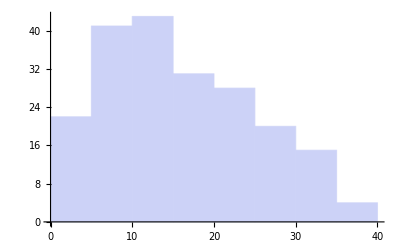

```mathematica
Histogram[EdgeLengths[w]]
```

```mathematica
EdgeLength[w,23]
```

11.4928